## Packages

### Almost always useful: different notebooks for different parameters/options, simulations versus analysing

### Easy to make: convert initialisation cells to package Trick: Edit --> Preferences --> Advanced --> Option Inspector --> Notebook options --> File Options --> Autogenerated package --> Manual

### Either put parameters/options before loading package or after

Example:

```mathematica
SetDirectory[NotebookDirectory[]];
<<MERA`
```

```mathematica
domodel[initIsing,6]
```

```mathematica
analysefile["Ising6.dat" ]
```

## Ncon

```mathematica
contract[a_,b_,links_]:=((*contract takes 2 tensors and the links which have to be contracted; it then rearranges (with Flatten) the tensors in such a way that the summation can be done using an ordinary dot product, i.e. A.B sums the last index of A with the first index of B*)
rearrangea=(List/@Select[Range[ArrayDepth[a]],m↦!MemberQ[links⟦;;,1⟧,m]])~Join~{links⟦;;,1⟧};
rearrangeb={links⟦;;,2⟧}~Join~(List/@Select[Range[ArrayDepth[b]],m↦!MemberQ[links⟦;;,2⟧,m]]);
Flatten[a,rearrangea].Flatten[b,rearrangeb]
)
out[a_,b_]:=contract[{a},{b},{{1,1}}]
```

```mathematica
trace[a_,links_,print_:True]:=(
If[print,Print["taking trace"]];
rearrange={links⟦;;,1⟧}~Join~{links⟦;;,2⟧}~Join~(List/@Select[Range[ArrayDepth[a]],m↦!MemberQ[Flatten[links⟦;;⟧],m]]);
Tr[Flatten[a,rearrange],Plus,2]
)
```

```mathematica
ncon[tensors_,legs_,sequence_]:=(
{tens1,legs1}={tensors,legs};
For[inc=1,inc≤Length[sequence],
{contr1,contr2}=Position[legs1,sequence⟦inc⟧]⟦;;,1⟧;(*tensors to be contracted*)
For[links={},(*look if we are to contract more than one leg*)
Length[links]+inc≤Length[sequence]&&{contr1,contr2}==Position[legs1,sequence⟦Length[links]+inc⟧]⟦;;,1⟧,
AppendTo[links,Position[legs1,sequence⟦Length[links]+inc⟧]⟦;;,2⟧]];

nlegs=Select[legs1⟦contr1⟧~Join~If[contr1≠contr2,legs1⟦contr2⟧,{}],!MemberQ[sequence⟦inc;;inc+Length[links]-1⟧,#]&]; (*combine legs*)

If[contr1==contr2,(*trace, remove tensor and add traced*)
tens1=Drop[tens1,{contr2}]~Join~{trace[tens1⟦contr1⟧,links,Length[tensors]>1]};
legs1=Drop[legs1,{contr2}]~Join~{nlegs};
,(*contract, remove tensor and add contracted*)
tens1=Drop[Drop[tens1,{contr2}],{contr1}]~Join~{contract[tens1⟦contr1⟧,tens1⟦contr2⟧,links]};
legs1=Drop[Drop[legs1,{contr2}],{contr1}]~Join~{nlegs}];
inc+=Length[links]];
While[Length[legs1]>1,(*outer product, only at end*)
tens1=Drop[tens1,2]~Join~{out[tens1⟦1⟧,tens1⟦2⟧]};
legs1=Drop[legs1,2]~Join~{legs1⟦1⟧~Join~legs1⟦2⟧}];
(*rearranging legs according to -legs*)
If[Length[legs1⟦1⟧]>0,Transpose[tens1⟦1⟧,-legs1⟦1⟧],tens1⟦1⟧]
)
ncon[tensors_,legs_]:=ncon[tensors,legs,Union[Select[Flatten[legs],#>0&]]]
```

IdentityMatrix, change order, translational operator

```mathematica
χ=18;
{w,u,operator}=Table[Random[],{3},{χ},{χ},{χ},{χ}];
```

```mathematica
AbsoluteTiming[nconp[{w,w*,w,w*,u,u*,operator},{{-1,1,2,3},{-3,1,2,9},{-2,4,11,12},{-4,10,11,12},{3,4,5,6},{7,8,9,10},{5,6,7,8}},{5,6,7,8,1,2,3,9,11,12,4,10}]//Dimensions]
```

## CUDA

```mathematica
cuda=False;
usecuda:=(
Needs["CUDALink`"];
cuda=True;)
CUDADot2[a_,b_]:=(
dima=Dimensions[a];
dimb=Dimensions[b];
If[Length[dima]>2||Length[dimb]>2,
ArrayReshape[CUDALink`CUDADot[Flatten[a,Length[dima]-2]//N,Flatten/@b//N],dima⟦;;-2⟧~Join~dimb⟦2;;⟧],
CUDALink`CUDADot[a//N,b//N]]
)
```

```mathematica
dot[a_,b_]:=If[cuda&&Dimensions[a]⟦-1⟧<2500,CUDADot2[a,b],a.b];
```

```mathematica
usecuda
```

## NDSolve and/or spectral methods

Solve linear ODE:

```mathematica
LDE=(2+x) y''[x]+y'[x]-20x y[x];
LDEboundary={y[-1]==5,y[1]==-1};
```

```mathematica
dsolLDE=y/.DSolve[{LDE==0,LDEboundary}//Flatten,y,{x,-1,1}]⟦1⟧
ndsolLDE=y/.NDSolve[{LDE==0,LDEboundary}//Flatten,y,{x,-1,1}]⟦1⟧
```

```mathematica
pl=Plot[dsolLDE[x]//Re,{x,-1,1.}]
```

```mathematica
initGrid[points_]:=(
nx=points;
x=N[Table[-Cos[(r π)/(nx-1)],{r,0,nx-1}]];
DSpec=NDSolve`FiniteDifferenceDerivative[1,x,DifferenceOrder->points-1]["DifferentiationMatrix"];
D2Spec=DSpec.DSpec;
x)
```

```mathematica
eqm=DiagonalMatrix[D[LDE,y''[x]]].D2Spec+DiagonalMatrix[D[LDE,y'[x]]].DSpec+DiagonalMatrix[D[LDE,y[x]]];
source=LDE/.y->(0&);
```

```mathematica
LinearSolve[eqm,-source]
```

```mathematica
eqm⟦1,;;⟧=Table[If[i==1,1,0],{i,nx}];
eqm⟦-1,;;⟧=Table[If[i==nx,1,0],{i,nx}];
{source⟦1⟧=-5,source⟦-1⟧=1};
```

```mathematica
function=LinearSolve[eqm,-source]
```

```mathematica
Show[pl,ListPlot[Thread[{x,function}]]]
```

```mathematica
function-dsolLDE[x]//ListPlot
```

```mathematica
grid=x;
x=.
```

```mathematica
ndsolLDE2=y/.NDSolve[{LDE==0,LDEboundary}//Flatten,y,{x,-1,1},StartingStepSize->10^-2,Method->{"FixedStep",Method->{"ExplicitRungeKutta","DifferenceOrder"->8,"StiffnessTest"->False}}]⟦1⟧
```

```mathematica
function-ndsolLDE2[grid]//ListPlot[#,PlotRange->All]&
```

Hint for time-dependent problem:

## Transforming functions/coordinate transformation

```mathematica
metric=({{0, 1, 0, 0, 0}, {1, -A[t,r], 0, 0, 0}, {0, 0, S[t,r]^2 Exp[-2B[t,r]], 0, 0}, {0, 0, 0, S[t,r]^2 Exp[B[t,r]], 0}, {0, 0, 0, 0, S[t,r]^2 Exp[B[t,r]]}});
coord={r,t,x1,x2,x3};
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"diffgeo.m";
```

SetDelayed::write: Tag Laplacian in Laplacian[scalar_ ? scalarQ] is Protected.

### We obtain Einstein' s equations :

```mathematica
EE=RicciTensor+4metric//Flatten//Union//Simplify
```

{0,-3/2 (B^(0,1)[t,r])^2-(3 S^(0,2)[t,r])/S[t,r],4-(3 A^(0,1)[t,r] S^(0,1)[t,r]+S[t,r] (A^(0,2)[t,r]+3 B^(0,1)[t,r] B^(1,0)[t,r])+6 S^(1,1)[t,r])/(2 S[t,r]),ⅇ^(-2 B[t,r]) (-2 S^(0,1)[t,r] (A[t,r] S^(0,1)[t,r]+2 S^(1,0)[t,r])+S[t,r]^2 (4+A^(0,1)[t,r] B^(0,1)[t,r]+A[t,r] B^(0,2)[t,r]+2 B^(1,1)[t,r])-S[t,r] (A^(0,1)[t,r] S^(0,1)[t,r]+A[t,r] (-3 B^(0,1)[t,r] S^(0,1)[t,r]+S^(0,2)[t,r])-3 S^(0,1)[t,r] B^(1,0)[t,r]-3 B^(0,1)[t,r] S^(1,0)[t,r]+2 S^(1,1)[t,r])),-1/2 ⅇ^B[t,r] (4 S^(0,1)[t,r] (A[t,r] S^(0,1)[t,r]+2 S^(1,0)[t,r])+S[t,r]^2 (-8+A^(0,1)[t,r] B^(0,1)[t,r]+A[t,r] B^(0,2)[t,r]+2 B^(1,1)[t,r])+S[t,r] (2 A^(0,1)[t,r] S^(0,1)[t,r]+A[t,r] (3 B^(0,1)[t,r] S^(0,1)[t,r]+2 S^(0,2)[t,r])+3 S^(0,1)[t,r] B^(1,0)[t,r]+3 B^(0,1)[t,r] S^(1,0)[t,r]+4 S^(1,1)[t,r])),(A[t,r] (3 A^(0,1)[t,r] S^(0,1)[t,r]+S[t,r] (-8+A^(0,2)[t,r]))-3 (S^(0,1)[t,r] A^(1,0)[t,r]+S[t,r] (B^(1,0)[t,r])^2-A^(0,1)[t,r] S^(1,0)[t,r]+2 S^(2,0)[t,r]))/(2 S[t,r])}

### Do a linearized approximations (look up black brane, or solve by near boundary analysis)

```mathematica
funcs={A,B,S};
```

```mathematica
linear=(f↦(f->(ToExpression[ToString[f]<>"0"][#1,#2]+ϵ ToExpression["δ"<>ToString[f]][#1,#2]&)))/@funcs
D[A[t,r],t]/.linear
```

{A→(ToExpression[ToString[A]<>0][#1,#2]+ϵ ToExpression[δ<>ToString[A]][#1,#2]&),B→(ToExpression[ToString[B]<>0][#1,#2]+ϵ ToExpression[δ<>ToString[B]][#1,#2]&),S→(ToExpression[ToString[S]<>0][#1,#2]+ϵ ToExpression[δ<>ToString[S]][#1,#2]&)}

A0^(1,0)[t,r]+ϵ δA^(1,0)[t,r]

```mathematica
blackbrane={B0->(0&),S0->(#2&),A0->(#2^2- 1/#2^2&)};
```

```mathematica
EEl=SeriesCoefficient[EE/.linear/.blackbrane,{ϵ,0,1}]/.δS->(0&)/.δA->(0&)//FullSimplify
```

{0,0,0,((-1+5 r^4) δB^(0,1)[t,r]+r ((-1+r^4) δB^(0,2)[t,r]+r (3 δB^(1,0)[t,r]+2 r δB^(1,1)[t,r])))/r,((1-5 r^4) δB^(0,1)[t,r]+r (-(-1+r^4) δB^(0,2)[t,r]-r (3 δB^(1,0)[t,r]+2 r δB^(1,1)[t,r])))/(2 r),0}

### Change coordinates to 1/r and B to B/z^4, which makes B regular at the boundary:

```mathematica
replrtou={Derivative[a_,b_][f_][t,r]->D[Derivative[a,0][f][t,1/r],{r,b}],f_[t,r]->f[t,u],r->1/u}
```

{f_^(a_,b_)[t,r]→∂_{r,b} f^(a,0)[t,1/r],f_[t,r]→f[t,u],r→1/u}

```mathematica
EElreg=-1/u^3 EEl⟦4⟧//.replrtou/.δB->(δBreg[#1,#2]#2^4&)//FullSimplify
```

16 u^3 δBreg[t,u]+(-5+9 u^4) δBreg^(0,1)[t,u]+u (-1+u^4) δBreg^(0,2)[t,u]+5 δBreg^(1,0)[t,u]+2 u δBreg^(1,1)[t,u]

### Now write time derivative equation numerically, as Bc∂_z (∂_t B)+Cc(∂_t B)+Sc=0, which is easy to solve spectrally

```mathematica
Bc=D[EElreg,Derivative[1,1][δBreg][t,u]]
Cc=D[EElreg,Derivative[1,0][δBreg][t,u]]
Sc=EElreg/.Derivative[1,a_][δBreg][t,u]->0//FullSimplify
```

2 u

5

16 u^3 δBreg[t,u]+(-5+9 u^4) δBreg^(0,1)[t,u]+u (-1+u^4) δBreg^(0,2)[t,u]

```mathematica
Snum[Bnum_]=Sc/.{δBreg[t,u]->Bnum,Derivative[0,1][δBreg][t,u]->DSpec.Bnum,Derivative[0,2][δBreg][t,u]->D2Spec.Bnum}
```

16 Bnum u^3+u (-1+u^4) D2Spec.Bnum+(-5+9 u^4) DSpec.Bnum

```mathematica
init[Breg_,points_]:=(
nu=points;
u=(N[Table[-Cos[(r π)/(nu-1)],{r,0,nu-1}]]+1)/2;
DSpec=NDSolve`FiniteDifferenceDerivative[1,u,DifferenceOrder->points-1]["DifferentiationMatrix"];
D2Spec=DSpec.DSpec;
Bnum=Breg[u])
u//Unprotect
```

```mathematica
init[u↦2u,30]
```

{0.,0.00586204,0.0233794,0.0523468,0.0924246,0.143143,0.203907,0.274005,0.352614,0.438813,0.531592,0.629862,0.732472,0.838218,0.945861,1.05414,1.16178,1.26753,1.37014,1.46841,1.56119,1.64739,1.726,1.79609,1.85686,1.90758,1.94765,1.97662,1.99414,2.}

```mathematica
dBregdt[Bnum_List]:=LinearSolve[DiagonalMatrix[Bc].DSpec+DiagonalMatrix[Cc+0 u],-Snum[Bnum]]
```

### Time stepping with NDSolve and/or ones favorite method (Runge-Kutta, Adams-Bashforth, implicit/explicit etc)

```mathematica
Timing[ndsol=NDSolve[{D[b[t],t]==dBregdt[b[t]],b[0]==Bnum},b,{t,0,8}]⟦1⟧;]
bi=b/.ndsol
```

{0.14063,Null}

InterpolatingFunction[{{0., 8.}}, <>]

```mathematica
tgrid=bi["Grid"]⟦;;,1⟧
```

{0.,0.0000873325,0.000174665,0.00310674,0.00603881,0.00897088,0.0172049,0.0254389,0.0336729,0.0419069,0.0583749,0.0748429,0.0913109,0.107779,0.124247,0.155397,0.186547,0.217697,0.248847,0.279997,0.311147,0.351171,0.391195,0.431218,0.471242,0.511266,0.55129,0.591313,0.602673,0.614033,0.625392,0.636752,0.648112,0.659471,0.665333,0.671194,0.677055,0.682916,0.688778,0.696231,0.703684,0.711138,0.718591,0.735571,0.752551,0.769531,0.786511,0.803491,0.82991,0.856329,0.882748,0.909167,0.935586,0.962005,0.994804,1.0276,1.0604,1.0932,1.126,1.1588,1.1916,1.19671,1.20183,1.20694,1.21205,1.21717,1.22228,1.23327,1.24425,1.25524,1.26622,1.27721,1.29569,1.31418,1.33266,1.35115,1.36963,1.38812,1.41732,1.44651,1.47571,1.50491,1.5341,1.5633,1.5925,1.61849,1.64448,1.67046,1.69645,1.72244,1.74843,1.77442,1.78041,1.7864,1.79239,1.79838,1.80437,1.81036,1.82171,1.83306,1.84441,1.85576,1.86711,1.88139,1.89567,1.90995,1.92422,1.9385,1.9614,1.9843,2.0072,2.0301,2.053,2.07591,2.10407,2.13223,2.1604,2.18856,2.21672,2.24489,2.27305,2.30121,2.32938,2.3633,2.39722,2.43114,2.46506,2.49899,2.53291,2.56683,2.57783,2.58882,2.59982,2.61081,2.62181,2.6328,2.65032,2.66783,2.68534,2.70285,2.72036,2.75163,2.7829,2.81416,2.84543,2.87669,2.90796,2.94681,2.98567,3.02453,3.06338,3.10224,3.1411,3.17995,3.18862,3.19728,3.20595,3.21462,3.22328,3.23195,3.24285,3.25376,3.26466,3.27557,3.28647,3.30363,3.32078,3.33794,3.35509,3.38322,3.41134,3.43946,3.46758,3.4957,3.55195,3.60819,3.66444,3.72068,3.77692,3.83317,3.8616,3.89004,3.91847,3.9469,3.97534,3.98812,4.0009,4.01369,4.02647,4.0648,4.10313,4.14147,4.1798,4.2252,4.27061,4.31602,4.36142,4.40683,4.45025,4.49367,4.53709,4.58051,4.62393,4.68326,4.74258,4.80191,4.86123,4.92056,4.94254,4.96452,4.9865,5.00848,5.02643,5.04438,5.06233,5.1022,5.14207,5.18194,5.22181,5.27193,5.32205,5.37216,5.42228,5.44674,5.4712,5.49566,5.5162,5.53675,5.55729,5.62024,5.68319,5.74613,5.80908,5.83085,5.85261,5.87438,5.91875,5.96312,6.00749,6.06611,6.12473,6.18335,6.19527,6.20718,6.21909,6.25337,6.28764,6.32191,6.34751,6.37311,6.39872,6.42472,6.45072,6.47673,6.49678,6.51682,6.53687,6.56469,6.59251,6.62033,6.66485,6.70937,6.7539,6.76872,6.78355,6.79838,6.82511,6.85183,6.87856,6.89954,6.92052,6.9415,6.97186,7.00223,7.03259,7.05974,7.08689,7.11403,7.16794,7.22185,7.27576,7.31704,7.35831,7.39958,7.42497,7.45035,7.47574,7.50916,7.54258,7.57599,7.60315,7.63031,7.65747,7.73975,7.82202,7.9043,7.92765,7.95099,7.97434,8.}

```mathematica
bi3d=Flatten[Table[{tgrid⟦i⟧,u⟦j⟧,bi[tgrid[[i]]][[j]]},{i,Length[tgrid]},{j,Length[u]}],1]//Interpolation
```

InterpolatingFunction[{{0., 8.}, {0., 1.}}, <>]

```mathematica
Plot3D[bi3d[x,y],{x,0.,8.},{y,0.,1.},PlotRange->All]
```

-Graphics3D-

### One clearly sees the lowest QNM:

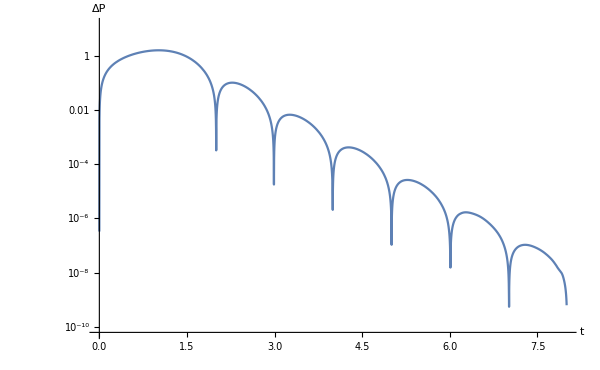

```mathematica
LogPlot[bi3d[t,0]//Abs,{t,0,8},BaseStyle->20,ImageSize->600,AxesLabel->{"t","ΔP"}]
```

My other favourite NDSolve methods :

```mathematica
NDSolve[....,StartingStepSize->10^-2,Method->{"FixedStep",Method->{"ExplicitRungeKutta","DifferenceOrder"->8,"StiffnessTest"->False}}]
```

For a time dependent problem:

```mathematica
NDSolve[....,StartingStepSize->10^-2,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->50,"MaxPoints"->50,"DifferenceOrder"->4}}]
```

### One could compute entanglement entropy (1506.02658)

```mathematica
u=.
```

```mathematica
σ={λ,λ2,λ3};
Xmu[λ_,λ2_,λ3_]:={u[λ],t[λ],x1[λ],λ2,λ3};
area=Integrate[Det[Table[D[Xmu@@σ,σ⟦i⟧].(metric/.u->u[λ]/.t->t[λ]).D[Xmu@@σ,σ⟦j⟧],{i,3},{j,3}]],λ]
```

∫(-ⅇ^(2 B[t[λ],u[λ]]) A[t[λ],u[λ]] S[t[λ],u[λ]]^4 t'[λ]^2-(2 ⅇ^(2 B[t[λ],u[λ]]) S[t[λ],u[λ]]^4 t'[λ] u'[λ])/u[λ]^2+S[t[λ],u[λ]]^6 x1'[λ]^2)ⅆλ

```mathematica
eq=D[D[area,D[#[λ],λ]],λ]-D[area,#[λ]]&/@{t,u,x1}
```